```mathematica
sig[x_]:=1/(1+E^(-x))
```

```mathematica
nn[x_,θ_,f_]:=Module[{w11,w12,w21,w22},
{w11,w12,w21,w22} = θ;
Return[f[w21*f[w11*x]+w22*f[w12*x]]];
]
```

```mathematica
gradient[x_,weights_]:=Module[{w11,w12,w21,w22,w},
w={w11,w12,w21,w22};
Return[D[nn[x,w,sig],{w}]]/.MapThread[#1->#2&,{w,weights}]
]
```

```mathematica
(*
Implement a simple backpropagation algorithm and print out the
weights along the way. Use this to really understand what is 
going on. And then use it as a way to generate data to test your
software with. Eg, you can generate the entire sequience of weights,
 outputs, and errors for 10, 100, or even 1000 iterations of 
backpropagation and use that to verify your python program.
*)
```

```mathematica
train[data_,init_]:=Module[{θ},
θ=init;

]
```

```mathematica
data={{2,.9},{1,.3},{-1,.4},{-2,.1}}
```

{{2,0.9},{1,0.3},{-1,0.4},{-2,0.1}}

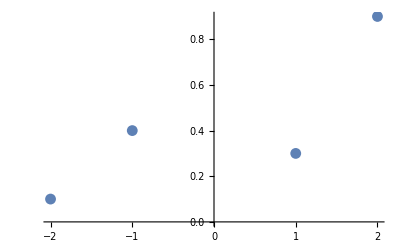

```mathematica
ListPlot[data]
```

```mathematica
θ = {.4,-.2,.6,.1};
```

```mathematica
adjust[.1, θ]
```

{0.00363252,0.000605601,0.123555,0.119921}

```mathematica
y[.1,θ,sig] -.47
```

0.11795

```mathematica
Δw= d/.{w11->.4,w12->-.2,w21->.6,w22->.1,x->.1}
```

{0.00363252,0.000605601,0.123555,0.119921}

```mathematica
y[.1,θ-Δw,sig] -.47
```

0.0880083